## 3.029 Spring 2022 Assignment 02 Due March 2nd at 1pm

## Classical Thermodynamics

## General Instructions Reminder

Notebooks should be submitted to canvas

You can choose to submit either a Wolfram Notebook (.nb), or  a Jupyter Notebook (.ipynb)

Please name your notebook using the following notation:
3029__Assignment-02__LASTNAME_FIRSTNAME.nb

Before submitting your notebook:

Make sure all your code runs from a fresh kennel 
Wolfram Notebook: Evaluation → Quit Kernel, Evaluation → Evaluate Notebook
Jupyter Notebook: Kernel → Restart & Run All

Delete all your output
Wolfram Notebook: Cell → Delete All Output
Jupyter Notebook: Cell → All Output → Clear

Tips to maximize your score:

Comment your code well using text cells/Markdown (not in-line comments)

Don’t include extraneous code and narrative that does not contribute to the answer

But feel free to keep a ‘scratch’ notebook as you develop your solutions

Make your graphics are aesthetically pleasing and easy to read

Notably: label your axes and use legible font sizes

## Maxwell Equal Area Construction (50 points)

### Introduction (Read only)

In Lecture 4, we investigated  the Van-der-Waals gas with equation of state

Remember we non-dimensionalized the equation of state, to obtain the expression

```mathematica
pNormalvdWEquationOfStateNormalized[vNormalized_,tNormalized_]=(3-9 vNormalized+8 tNormalized vNormalized^2)/(vNormalized^2 (-1+3 vNormalized));
```

And plotted various isotherms (i.e. P-V diagrams at constant T)

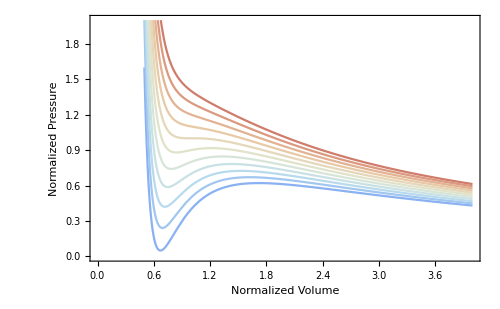

```mathematica
isothermPlot=With[ {curves = Table[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{tNormalized,0.85,1.1,0.025}]},
Plot[curves,{vNormalized,0.5,4},]
]
```

Below the critical temperature, the equation of state admits three volume for certain pressures

We said that the intermediate volume is always unstable

The instability proceeds as the volume expands (or shrinks) towards the higher (lower) stable values.

The stable volumes (i.e., more dense or at smaller volume) are in equilibrium with each other.

These are the volumes corresponding to the two sides of the vapor-liquid line in the P-T diagram.

In Lecture 5, we introduced the (normalized) Helmholtz and Gibbs Free energies for the vDW gas

And used their convexity to extract the stable volumes

This allowed us to make linked visualizations of the sort

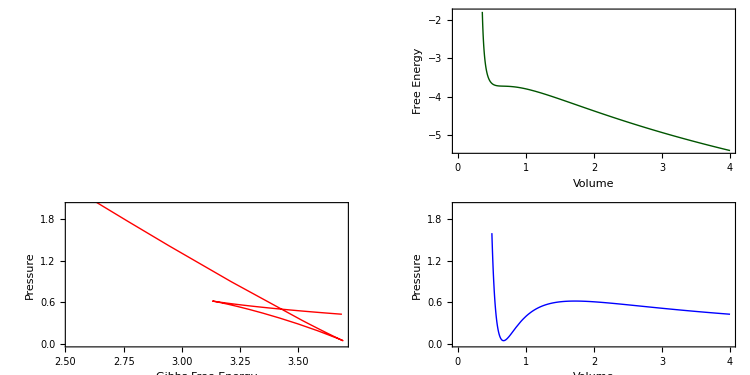

In this assignment you’ll use another geometrical construction called “Maxwell’s equal area” construction
to obtain the stable volumes, and finish the visualization

### Chemical Equilibrium (Read only)

Since this instability describes the Liquid-Gas phase transition, we must have at-least two-phases in the system

I.e. the fundamental thermodynamic relation for our system looks like:

In chemical and thermal equilibrium, the requirement for two phases to co-exist at constant temperature is given by the chemical potential equality

Note: the subscript j still refers to the component, of which we only have one (say H_2 0). The superscript refers to the phase of the component (say water vs ice). 
We will drop the subscript j in what follows

At isothermal conditions, the infinitesimal change in the chemical potential is given by:

and the Gibbs-Duhem equation is given by:

Combining eqs. (4) and (5), we can relate the molar volume of each phase to the variation of its chemical potential with pressure.
Starting from the liquid phase, we can integrate the molar volume variation to obtain the chemical potential.

When we reach the gaseous phase, the chemical potential is equal that of the liquid, and thus the integral must vanish.

Thermodynamically, this means that there exists an equilibrium pressure at which the work along an isothermal path
will equal the work along an isobaric path, The idea is illustrated graphically below:

The blue region represents the isothermal work and the yellow region is the isobaric work.

### Graphical Construction (25 points)

Graphically, this means the areas 'above' and 'below' the equilibrium pressure must be equal.
This is the basis for the Maxwell equal area construction.

Due to the cubic root of the equation of state, this cannot be solved analytically and we proceed to compute this equilibrium pressure numerically.
The two equations we want to solve for are:

Construct a function that takes a temperature and returns the molar volumes of the two phases their equilibrium pressure.

Hint: You may need to use a numerical function, and make an educated initial guess of the stable volumes, e.g. like the `commonTangentPoints` function we used in L05

Make a list of {P,T,{V^liq,V^gas}} for multiple values of T  in 0 <T <1

### Co-existence Phase Diagrams (10 points)

In the P-T plane, plot the curve of co-existence values of the equilibrium P and T

Comment on your result

In the T-V plane, draw (tie-)lines at constant temperature connecting the two equilibrium volumes

Comment on your result

### Educational Widget (15 points)

Complete the linked-visualization widget we started constructing in L05, to include the Maxwell-Equal-Area constuction

Hint: Write a single function which accepts a normalized temperature and returns a static plot
e.g. like the `linkedVisualization[tNormalized_]` function we wrote in L05

You might consider also adding the following:

The spinode region in the PV diagram we saw in L04

Dotted vertical (equilibrium volumes) and horizontal (equilibrium pressure) lines connecting the various panels

Use the top-left quadrant to add explanatory text about the widget (similar to an infographic)

## Virial Coefficients (25 points)

### Introduction (Read Only)

Van der Waals postulated his equation of state based on experimental observations of reduced gas pressures, which hinted to the presence of (attractive) interactions between molecules.

In general, we can express deviations away from gas ideality as a series expansion in increasing orders of density, n =N/V.

where the temperature-dependent coefficients, B_i(T), are known as virial coefficients.

Truncating eq. (8) to second order in the density and re-arranging gives:

Taylor-expanding the last parentheses to linear order, we recover Van der Waals’ equation of state:

The virial coefficients stem from intermolecular interactions

as such it is reasonable to expect to derive these with knowledge of the intermolecular interaction function.

The second virial coefficient is given by (I will try and post an optional reading notebook on how to derive this using diagrammatic methods):

Where U(r) is the interatomic potential

### Interatomic Potentials (10 points)

Compute the second virial coefficient (symbolically as a function of temperature) for the following interatomic potentials

Hard Sphere Potential

U(r) = Piecewise[{{∞, r<= r0}, {-(u_0(r_0/r))^6, r>r_0}}]

Piecewise Constant Potential

U(r) = Piecewise[{{∞, 0<r<= a}, {-ϵ, a<r<b}, {0, b<r<∞}}]

Comment on your results at both the high and low temperature limits

### Dieterici’s Equation (15 points)

Another popular equation of state is Dieterici’s equation:

Non-dimensionalize Dieterici’s equation of state

Hint: Use a similar procedure like we did in L04 for the Van der Waals Equation of State

Comment on the non-dimensional ratio

How does this compare to the Van der Waals ratio?

Using data from here, compute the ratio for some actual gases and compare against the two models

Reproduce the isotherms + spinode construction below for Dieterici’s equation

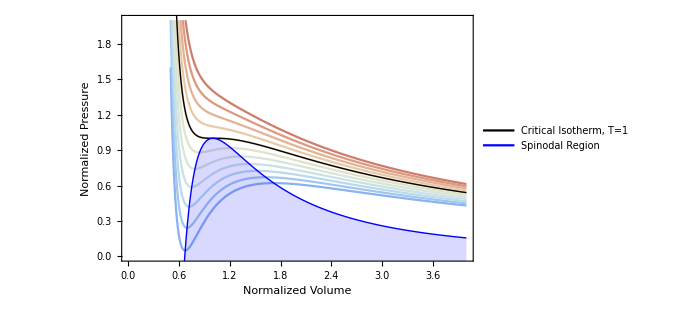

```mathematica
spinodeVDW[vNormalized_]=(-2+3 vNormalized)/vNormalized^3;
Show[isothermPlot,Plot[{pNormalvdWEquationOfStateNormalized[vNormalized,1],spinodeVDW[vNormalized]},{vNormalized,0.5,4},]]
```

## Tensorial Physical Properties (25 points)

As we mentioned in class, there are two types of symmetries tensors describing physical processes possess:

“Intrinsic” tensor symmetries

Crystal symmetries

### Intrinsic Tensor Symmetries (10 points)

“Intrinsic” tensor symmetries refer to phase factors one obtains by interchanging some of the tensor indices

E.g. For a rank-2 tensor ρ_ij

If swapping the first and second index,  leaves the tensor unchanged,  ρ_ij=ρ_ji, then we say the tensor is symmetric under i ↔ j permutation
and we denote this using parentheses around the indices ρ_(ij)

If swapping the first and second index, negates the tensor, ρ_ij=-ρ_ji,  then we say the tensor is antisymmetric under i ↔ j permutation
and we denote this using square parentheses around the indices ρ_[ij]

Using this notation, write down the tensor rank, defining equation, and intrinsic symmetries of the following tensors:

Strain Tensor, ϵ

Pyroelectric Tensor, p

Conductivity Tensor, σ

Viscosity Tensor, η

Piezoelectricity Tensor, d

Elastic Stiffness Tensor, C

Hint: An excellent reference for this is Nye’s Physical Properties of Crystals (which is available at the library). 
Googling is of-course also acceptable

Express the most-general tensors for the physical properties above using `SymmetrizedArray` like we did in lecture and list the number of independent components

E.g. the stiffness tensor, C, in 3D

```mathematica
MatrixForm[
stiffnessTensor=
With[{symbolName=c,d=3},
Normal[
SymmetrizedArray[pos_:>symbolName@@pos,{d,d,d,d},{
{Cycles[{{1,2}}],1},
{Cycles[{{3,4}}],1},
{Cycles[{{1,3},{2,4}}],1}
}
]]]]
```

((c[1,1,1,1] | c[1,1,1,2] | c[1,1,1,3]
c[1,1,1,2] | c[1,1,2,2] | c[1,1,2,3]
c[1,1,1,3] | c[1,1,2,3] | c[1,1,3,3]) | (c[1,1,1,2] | c[1,2,1,2] | c[1,2,1,3]
c[1,2,1,2] | c[1,2,2,2] | c[1,2,2,3]
c[1,2,1,3] | c[1,2,2,3] | c[1,2,3,3]) | (c[1,1,1,3] | c[1,2,1,3] | c[1,3,1,3]
c[1,2,1,3] | c[1,3,2,2] | c[1,3,2,3]
c[1,3,1,3] | c[1,3,2,3] | c[1,3,3,3])
(c[1,1,1,2] | c[1,2,1,2] | c[1,2,1,3]
c[1,2,1,2] | c[1,2,2,2] | c[1,2,2,3]
c[1,2,1,3] | c[1,2,2,3] | c[1,2,3,3]) | (c[1,1,2,2] | c[1,2,2,2] | c[1,3,2,2]
c[1,2,2,2] | c[2,2,2,2] | c[2,2,2,3]
c[1,3,2,2] | c[2,2,2,3] | c[2,2,3,3]) | (c[1,1,2,3] | c[1,2,2,3] | c[1,3,2,3]
c[1,2,2,3] | c[2,2,2,3] | c[2,3,2,3]
c[1,3,2,3] | c[2,3,2,3] | c[2,3,3,3])
(c[1,1,1,3] | c[1,2,1,3] | c[1,3,1,3]
c[1,2,1,3] | c[1,3,2,2] | c[1,3,2,3]
c[1,3,1,3] | c[1,3,2,3] | c[1,3,3,3]) | (c[1,1,2,3] | c[1,2,2,3] | c[1,3,2,3]
c[1,2,2,3] | c[2,2,2,3] | c[2,3,2,3]
c[1,3,2,3] | c[2,3,2,3] | c[2,3,3,3]) | (c[1,1,3,3] | c[1,2,3,3] | c[1,3,3,3]
c[1,2,3,3] | c[2,2,3,3] | c[2,3,3,3]
c[1,3,3,3] | c[2,3,3,3] | c[3,3,3,3]))

```mathematica
Variables[stiffnessTensor]//Length
```

21

### Crystal Symmetries (15 points)

In addition to intrinsic symmetries, we also saw Neumann’s principle constrains the independent components further according to:

“The symmetry elements of any physical property of a crystal must include the symmetry elements of the point group of the crystal”

Express Neumann’s principle using transformation laws for each of the physical properties above

Express the independent components of the conductivity tensor, σ, for the following point groups:

Point Group 11 (International Symbol: 4m)

Point Group 12 (International Symbol: 422)

Point Group  23 (International Symbol: 6/m)

Point Group 30 (International Symbol: 432)

Comment on the differences b/w certain point groups

Express the independent components of the piezoelectricity tensor, d, for the following point groups:

Point Group 11 (International Symbol: 4m)

Point Group 12 (International Symbol: 422)

Point Group  23 (International Symbol: 6/m)

Point Group 30 (International Symbol: 432)

Comment on the differences b/w certain point groups

Hint:  The following imports a Dataset with 3D Point Group data

```mathematica
Keys[pointGroupsAsc=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/gvarnavi/3D-point-groups-association"](https://www.wolframcloud.com/obj/gvarnavi/3D-point-groups-association)]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

E.g. The 6^th point group:

has International symbol 222

belongs to the Orthorhombic crystal system

and has the following 4 symmetry operations

```mathematica
Keys[pointGroupsAsc[6]]
```

{International Symbol,Schoenflies,Crystal System,Order,Symmetry Generators,Symmetries,Descriptions}

```mathematica
Dataset[pointGroupsAsc[[6,{"International Symbol","Crystal System","Descriptions"}]]]
```